### Response Time Distributions in Tandem G-Networks

```mathematica
ClearAll["Global`*"]
```

For a two - queue tandem network formed of G - queues (with positive and negative arrivals at each node), the function below computes the transform of the response time distribution at transform parameter value s. Service rates at the two nodes are μ1 and μ2 ,  positive and negative arrival rates at the two nodes are λ1p, λ1m and λ1p, λ2m at nodes 1 and 2 respectively.

```mathematica
(*Debugging printing*)
Attributes[PrintDebug]={HoldAll};
PrintDebug[expr_]:=Block[{debugPrint=Print},expr];

(*Fredhom solver*)
Options[FredholmKind2]={Method->Automatic};
FredholmKind2[{y1_,y2_,lambda_,k_,g_},n_?IntegerQ,OptionsPattern[]]:=Block[{step,SI,GI,KMatrix,W,DMatrix,f,deltaX,delta},
(* http://mathematica.stackexchange.com/questions/11594/integral-equation-numerical-solution-with-ndsolve *)
step=(y2-y1)/n;
SI=Range[y1,y2,step];
GI=g/@SI;
KMatrix=Outer[k,SI,SI];
W={step/2}~Join~ConstantArray[step,n-1]~Join~{step/2};
DMatrix=DiagonalMatrix[W];
f=If[OptionValue[Method]===NIntegrate,deltaX[y_?NumericQ]:=W.(k[y,#]&/@SI)-NIntegrate[k[y,t],{t,y1,y2}];
(*If the integral is expensive ParallelMap is an option here*)delta=deltaX/@SI;
Interpolation[Transpose@{SI,LinearSolve[IdentityMatrix[n+1]+lambda*(DiagonalMatrix[delta]-KMatrix.DMatrix),GI]}],Interpolation[Transpose@{SI,LinearSolve[IdentityMatrix[n+1]-lambda*(KMatrix.DMatrix),GI]}]];
Return[f];
];

(*Laplace transform at transform parameter value s*)
Wstar[s_,λ1p_:3,λ1m_:2,λ2p_:0,λ2m_:2,μ1_:2,μ2_:1]:=Module[{y1s,λ1,λ2,ρ1,ρ2,α,a1,a2,y,y1,y2,y3,y4,yp,ym,ysm,zp,zm,zsm,lambdaz,Kpartz,gfun,fz,YYz,Cz,Kernelz,Hz,h,Gtilde},
If[Im[s]≠0||s<0,Return["ERROR: s must be real and non-negative"]];
λ1=λ1p+λ1m;λ2=λ2p+λ2m;(*p.226*)ρ1=λ1p/(λ1m+μ1);ρ2=(μ1 ρ1+λ2p)/(λ2m+μ2);(*p.227*)
If[ρ1≥1,Return["ERROR: Node 1 utilization ≥1"]];
If[ρ2≥1,Return["ERROR: Node 2 utilization ≥1"]];
α=s+λ1+λ2+μ1+μ2(1-ρ2);(*p.234*)
{a1,a2}=y/.NSolve[α y-λ2m y^2-λ2p==0,y]//Chop;(*Lemma 1.1*)
debugPrint["Checking a1, a2 values: ",{a1,a2}];

{y1,y2,y3,y4}=y/.NSolve[(α y-λ2m y^2-λ2p)^2-4λ1p y(λ1m y+μ1)==0,y]//Chop;(*Lemma 1.1*)
debugPrint["Checking y1, y2, y3, y4 values: ",{y1,y2,y3,y4}];

yp[z_]:=(α z-λ1p-λ1m z^2+Sqrt[(α z-λ1p-λ1m z^2)^2-4λ2m z^2(λ2p+μ1 z)])/(2λ2m z);(*p.235, [13]*)
ym[z_]:=(α z-λ1p-λ1m z^2-Sqrt[(α z-λ1p-λ1m z^2)^2-4λ2m z^2(λ2p+μ1 z)])/(2λ2m z);(*p.235, [13]*)
ysm[z_]:=If[Abs[yp[z]]≤Abs[ym[z]],yp[z],ym[z]]; (*choose smallest modulus value*)
zp[y_]:=(α y-λ2m y^2-λ2p+ⅈ Sqrt[4λ1p y(λ1m y+μ1)-(α y-λ2m y^2-λ2p)^2])/(2(λ1m y+μ1));(*p. 238, [18]*)
zm[y_]:=(α y-λ2m y^2-λ2p-ⅈ Sqrt[4λ1p y(λ1m y+μ1)-(α y-λ2m y^2-λ2p)^2])/(2(λ1m y+μ1));(*p. 238, [18]*)
zsm[y_]:=If[Abs[zp[y]]≤Abs[zm[y]],zp[y],zm[y]]; (*choose smallest modulus value*)
y1s=Min[y/.Solve[λ1m y^2-(s+λ1+μ1(1-ρ1))y+λ1p==0,y]]//N;(*p.229 Theorem 1*)
If[y1s≥1,Return["ERROR: y1[s]≥1"]];
debugPrint["Checking y1[s] value: ",y1s];
debugPrint["Checking z[y] values: ",{zp[y1],zp[y2],zp[y3],zp[y4]}];

ysvals=yy/.NSolve[s+λ1+λ2+μ1+μ2(1-ρ2)-λ1p/y1s-λ1m y1s-λ2p/yy-λ2m yy-μ1 y1s/yy==0,yy];(*p.240*)
ysval=If[Abs[ysvals[[1]]]≤Abs[ysvals[[2]]],ysvals[[1]],ysvals[[2]]];
If[(λ1p ysval)/((λ1m ysval+μ1)y1s)>y1s,debugPrint["y1[s] is inside R_L"],debugPrint["y1[s] is inside R_Le\\L ∩ R_C"]];
n=100;
(*Terms for Fredholm integral equation specified in equation [17], p.238*)
lambdaz=-μ1 λ2m/(2π ⅈ);
Kpartz[y_,t_]:=((λ1m y+μ1)(zp[y]-zm[y]))/(λ1p μ1^2+(λ2m y t-λ2p)(λ2m t(λ1m y+μ1)+μ1(λ2m y-α)-λ1m λ2p));
gfun[y_]:=μ2 y/(1-y)(zp[y]/((1-zp[y])(zp[y]-ρ1))-zm[y]/((1-zm[y])(zm[y]-ρ1)));(*p.238*)
fz=FredholmKind2[{y1,y2,lambdaz,Kpartz,gfun},n,Method->Automatic];
debugPrint["Solution to Fredholm equation:"];
debugPrint[Plot[{Re[fz[yyy]],Im[fz[yyy]]},{yyy,y1,y2},{PlotStyle->Thick,PlotLegends->{"Real part","Imaginary part"},AxesLabel->{"y from y1 to y2"},PlotRange->All}]];
(*YYz[y_]:=D[zp[y],y]/zp[y] + D[zm[y],y]/zm[y];*)
Cz=Re[NIntegrate[μ1*fz[y]/(2*Pi*I*y*(y (λ2m+λ1m)+μ1)),{y,y1,y2}]];
(*Cz=NIntegrate[YYz[y]*fz[y]/(2*Pi*I),{y,y1,y2}]//Chop;*)
Kernelz[zz_,yy_]:=(D[zp[y],y]/(zp[y]-zz) +D[zm[y],y]/(zm[y]-zz))/.{y->yy};
Hz[zz_]:=Cz-NIntegrate[Kernelz[zz,y]*fz[y]/(2*Pi*I),{y,y1,y2}];
h[zz_]:=μ2 ysm[zz]/(1-ysm[zz])(zz/((1-zz)(zz-ρ1))-((λ1p ysm[zz])/(zz(λ1m ysm[zz]+μ1)))/((1-(λ1p ysm[zz])/(zz(λ1m ysm[zz]+μ1)))((λ1p ysm[zz])/(zz(λ1m ysm[zz]+μ1))-ρ1)));(*p.234 using z^sigma from p.235*)
(*debugPrint[ListLinePlot[{Table[{zz,Hz[zz]},{zz,Re[zp[y1]],Re[zp[y2]],0.01}],Table[{zz,h[zz]+Hz[(λ1p ysm[zz])/((λ1m ysm[zz]+μ1)zz)]},{zz,Re[zp[y2]],Re[zp[y3]],0.01}]},{PlotStyle->Thick,PlotLegends->{"Hz[z]","h[z]+H[z]"},AxesLabel->{"H[z] from z1 to z2, then z2 to z3"},PlotRange->All}]];*)
Gtilde[zz_]:=Block[{},(*For real valued z only*)
(*p.239, first case*)
If[zz> Re[zp[y1]]&&zz<Re[zp[y2]],
debugPrint["As y1[s] is in R_L, use equation [19] for H[z]"];
debugPrint["Hz[zz]=",Hz[zz]];
debugPrint["(λ1p ysm[zz])/((λ1m ysm[zz] + μ1) zz)=",(λ1p ysm[zz])/((λ1m ysm[zz]+μ1)zz)];
Return[(zz-ρ1)/(zz(μ1 zz+λ2p))Hz[zz]]];
(*p.239, second case*)
If[((zz<Re[zp[y1]]&&zz>Re[zp[y4]])||(zz>Re[zp[y2]]&&zz<Re[zp[y3]]))&&(zz<ρ1),(*RC defined on p.234*)
debugPrint["As y1[s] is in R_Le\\L ∩ R_C, use alternative result for H[z]"];
debugPrint["zz=",zz];
debugPrint["h[zz]=",h[zz]];
debugPrint["(λ1p ysm[zz])/((λ1m ysm[zz] + μ1) zz)=",(λ1p ysm[zz])/((λ1m ysm[zz]+μ1)zz)];
debugPrint["Hz[lots]=",Hz[(λ1p ysm[zz])/((λ1m ysm[zz]+μ1)zz)]];

Return[(zz-ρ1)/(zz(μ1 zz+λ2p))(h[zz]+Hz[(λ1p ysm[zz])/((λ1m ysm[zz]+μ1)zz)])];
(*Catch remaining values*)
Return["ERROR: Unexpected value for y1[s] (outside considered region)."]];
];
(*Return W*(s),p.239*)
Return[((1-ρ1)(1-ρ2)μ1 y1s)/λ1p Gtilde[y1s]//Chop]; 
];
(*Exact value*)
ProbabilityOfNotBeingKilled[λ1p_:3,λ1m_:2,λ2p_:0,λ2m_:2,μ1_:2,μ2_:1]:=Module[{λ1,λ2,ρ1,ρ2},
λ1=λ1p+λ1m;λ2=λ2p+λ2m;(*p.226*)ρ1=λ1p/(λ1m+μ1);ρ2=(μ1 ρ1+λ2p)/(λ2m+μ2);(*p.227*)
If[ρ1≥1,Return["ERROR: Node 1 utilization ≥1"]];
If[ρ2≥1,Return["ERROR: Node 2 utilization ≥1"]];
Return[(μ1 μ2)/((λ1m+μ1)(λ2m+μ2))];
];
MeanResponseTimeNoNegativeCustomers[λ1p_:3,λ1m_:2,λ2p_:0,λ2m_:2,μ1_:2,μ2_:1]:=Module[{},
Return[1/(μ1-λ1p)+1/(μ2-λ1p-λ2p)];
];
```

#### Highlight problems with first branch of H[z]

```mathematica
Wstar[0.001,3,2,0,2,2,1]
```

0.166163

```mathematica
ProbabilityOfNotBeingKilled[3,2,0,2,2,1]//N
```

0.166667

```mathematica
Wstar[0.001,3,2,1,2,2,1]
```

0.000106664

```mathematica
ProbabilityOfNotBeingKilled[3,2,1,2,2,1]//N
```

0.166667

#### Checking values computed in the appendix

These values all agree with those quoted in the appendix of the paper and of Pitels’ thesis.

Checking a1, a2 values: {0,7.25}

Checking y1, y2, y3, y4 values: {0,0.134435,4.54439,9.82117}

Checking y1[s] value: 0.303228

Checking z[y] values: {0,0.421611+0. ⅈ,1.10881+1.52034×10^-8 ⅈ,-1.16678+0. ⅈ}

y1[s] is inside R_L

Solution to Fredholm equation:

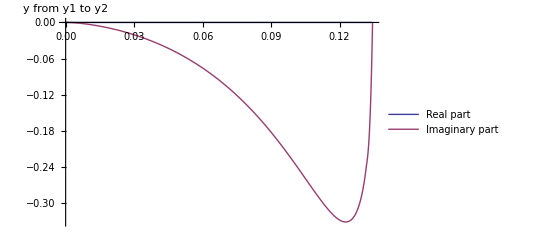

As y1[s] is in R_L, use equation [19] for H[z]

0.00488819

```mathematica
Wstar[5]//PrintDebug
```

Checking a1, a2 values: {0,6.91629}

Checking y1, y2, y3, y4 values: {0,0.33586,4.2507,9.24602}

Checking y1[s] value: 0.232558

Checking z[y] values: {0.+0. ⅈ,0.303932+0. ⅈ,0.750303+2.23274×10^-8 ⅈ,-0.858469+1.90035×10^-8 ⅈ}

y1[s] is inside R_L

Solution to Fredholm equation:

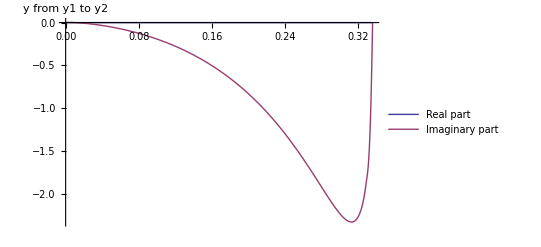

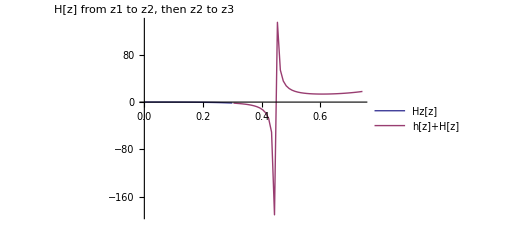

As y1[s] is in R_L, use equation [19] for H[z]

Hz[zz]=-0.616528+0. ⅈ

(λ1p ysm[zz])/((λ1m ysm[zz] + μ1) zz)=0.447917

7.16892×10^-7

```mathematica
Wstar[0.00001,1,1,0,1,3.3,1]//PrintDebug
```

Checking a1, a2 values: {0,5.30002×10^6}

Checking y1, y2, y3, y4 values: {0,0.469914,5.29747×10^6,5.30257×10^6}

Checking y1[s] value: 0.303028

Checking z[y] values: {0.+0. ⅈ,0.377357+0. ⅈ,784.934+0. ⅈ,-785.139+0. ⅈ}

y1[s] is inside R_L

Solution to Fredholm equation:

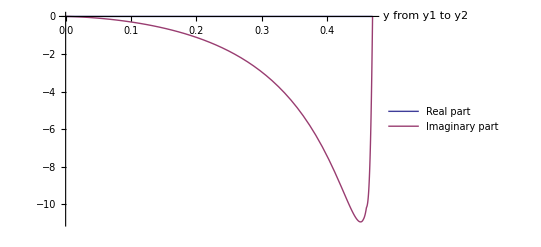

As y1[s] is in R_L, use equation [19] for H[z]

Hz[zz]=-3.14552-1.46518×10^-8 ⅈ

(λ1p ysm[zz])/((λ1m ysm[zz] + μ1) zz)=0.5

Checking a1, a2 values: {0,5.30001×10^6}

Checking y1, y2, y3, y4 values: {0,0.469916,5.29746×10^6,5.30256×10^6}

Checking y1[s] value: 0.303029

Checking z[y] values: {0.+0. ⅈ,0.377358+4.5155×10^-9 ⅈ,784.962+0.0236479 ⅈ,-785.107+0.0160507 ⅈ}

y1[s] is inside R_L

Solution to Fredholm equation:

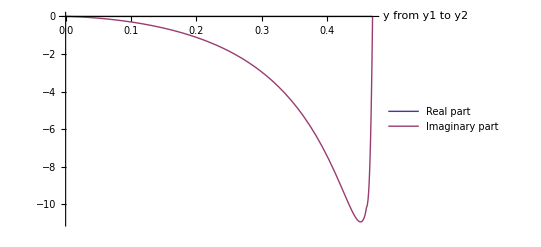

As y1[s] is in R_L, use equation [19] for H[z]

Hz[zz]=-3.14553+0. ⅈ

(λ1p ysm[zz])/((λ1m ysm[zz] + μ1) zz)=0.5

-13.3442

```mathematica
-(Wstar[0.00002,1,0.000001,0,0.000001,3.3,2]-Wstar[0.00001,1,0.000001,0,0.000001,3.3,2])/0.00001//PrintDebug
```

Checking a1, a2 values: {0,6.9163}

Checking y1, y2, y3, y4 values: {0,0.335859,4.25071,9.24603}

Checking y1[s] value: 0.232557

Checking z[y] values: {0.+0. ⅈ,0.303931+0. ⅈ,0.750303+2.95363×10^-8 ⅈ,-0.858469+1.90035×10^-8 ⅈ}

y1[s] is inside R_L

Solution to Fredholm equation:

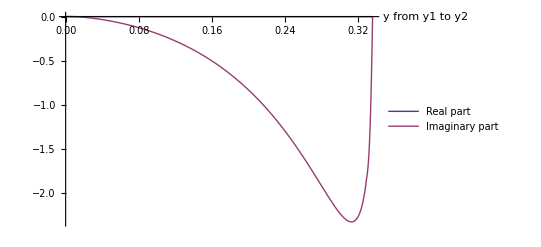

As y1[s] is in R_L, use equation [19] for H[z]

Hz[zz]=-0.616526-9.91126×10^-10 ⅈ

Checking a1, a2 values: {0,6.91629}

Checking y1, y2, y3, y4 values: {0,0.33586,4.2507,9.24602}

Checking y1[s] value: 0.232558

Checking z[y] values: {0.+0. ⅈ,0.303932+0. ⅈ,0.750303+2.23274×10^-8 ⅈ,-0.858469+1.90035×10^-8 ⅈ}

y1[s] is inside R_L

Solution to Fredholm equation:

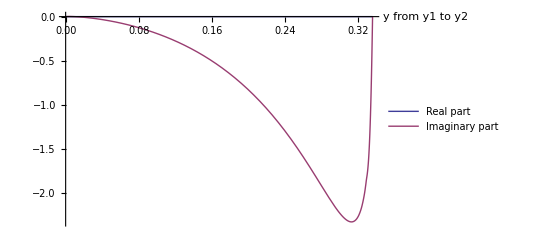

As y1[s] is in R_L, use equation [19] for H[z]

Hz[zz]=-0.616528+0. ⅈ

-0.0716888

```mathematica
-(Wstar[0.00002,1,1,0,1,3.3,1]-Wstar[0.00001,1,1,0,1,3.3,1])/0.00001//PrintDebug
```

Checking a1, a2 values: {0.0985077,10.1515}

Checking y1, y2, y3, y4 values: {0.0521296,0.195677,8.00379,12.2484}

Checking y1[s] value: 0.135792

Checking z[y] values: {-0.222591+0. ⅈ,0.404542+0. ⅈ,0.942834+2.64798×10^-8 ⅈ,-0.961519+1.27251×10^-8 ⅈ}

y1[s] is inside R_L

Solution to Fredholm equation:

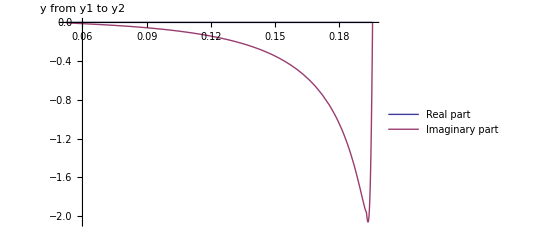

As y1[s] is in R_L, use equation [19] for H[z]

0.00320654

```mathematica
Wstar[5,1,1,1,1,1,1]//PrintDebug
```

#### Evaluating near zero (to compute moments)

We would expect values near s = 0 to be near

```mathematica
Probability of not being killed: p. 232
(μ1 μ2)/((λ1m+μ1)(λ2m+μ2))=(2*1)/((2+2)(2+1))=1/6;
```

```mathematica
Table[-(Wstar[2 h]-Wstar[h])/(h),{h,{0.00001,0.000001,0.0000001,0.00000001}}]
```

{0.50201,0.502041,0.502044,0.502044}

```mathematica
Table[-(Wstar[2 h]-Wstar[h])/(h),{h,{0.005,0.002,0.0001,0.0009,0.0008,0.00007}}]
```

{0.485175,0.495177,0.501697,0.498934,0.499278,0.501801}

```mathematica
Table[-(Wstar[2 h]-Wstar[h])/(h),{h,{1,0.5,0.1,0.05,0.01}}]
```

{0.0178745,0.045274+7.46718×10^-9 ⅈ,0.297088,0.370068,0.469262}

```mathematica
-(Wstar[0.0002,1,0.01,1,0.01,2,4]-Wstar[0.0001,1,0.01,1,0.01,2,4])/0.0001
```

-3.39062-0.0244031 ⅈ

```mathematica
Table[{{μ1,Wstar[0.0001,3,2,1,2,μ1,4]}},{μ1,1.1,6,0.1}]
```

{{{1.1,0.235923}},{{1.2,0.24969}},{{1.3,0.262422}},{{1.4,0.274357}},{{1.5,0.285592}},{{1.6,0.296193}},{{1.7,0.306217}},{{1.8,0.31571}},{{1.9,0.324714}},{{2.,0.333266}},{{2.1,0.3414}},{{2.2,0.349146}},{{2.3,0.35653}},{{2.4,0.363576}},{{2.5,0.370306}},{{2.6,0.376738}},{{2.7,0.382886}},{{2.8,0.388752}},{{2.9,0.394303}},{{3.,0.399154}},{{3.1,0.0000952904}},{{3.2,0.0000883785}},{{3.3,0.0000794226}},{{3.4,0.0000701661}},{{3.5,0.0000614585}},{{3.6,0.0000536716}},{{3.7,0.0000469071}},{{3.8,0.0000411242}},{{3.9,0.000036218}},{{4.,0.000032065}},{{4.1,0.0000285451}},{{4.2,0.0000255515}},{{4.3,0.0000229933}},{{4.4,0.0000207955}},{{4.5,0.0000188965}},{{4.6,0.0000172462}},{{4.7,0.0000158041}},{{4.8,0.000014537}},{{4.9,0.0000134181}},{{5.,0.0000124252}},{{5.1,0.0000115402}},{{5.2,0.0000107479}},{{5.3,0.0000100358}},{{5.4,9.39335×10^-6}},{{5.5,8.81173×10^-6}},{{5.6,8.28344×10^-6}},{{5.7,7.80211×10^-6}},{{5.8,7.36227×10^-6}},{{5.9,6.95926×10^-6}},{{6.,6.58904×10^-6}}}

Checking a1, a2 values: {0.0865756,5.7753}

Checking y1, y2, y3, y4 values: {0.0301688,0.32775,3.03492,8.33091}

Checking y1[s] value: 0.967659

Checking z[y] values: {-0.279285+0. ⅈ,0.748396+0. ⅈ,1.12688+0. ⅈ,-1.18621+0. ⅈ}

y1[s] is inside R_Le\L ∩ R_C

Solution to Fredholm equation:

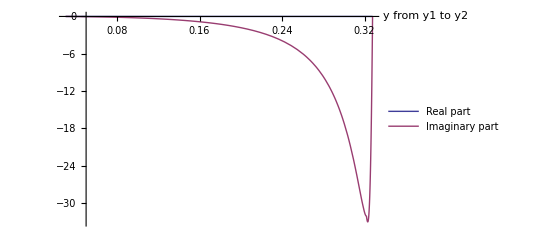

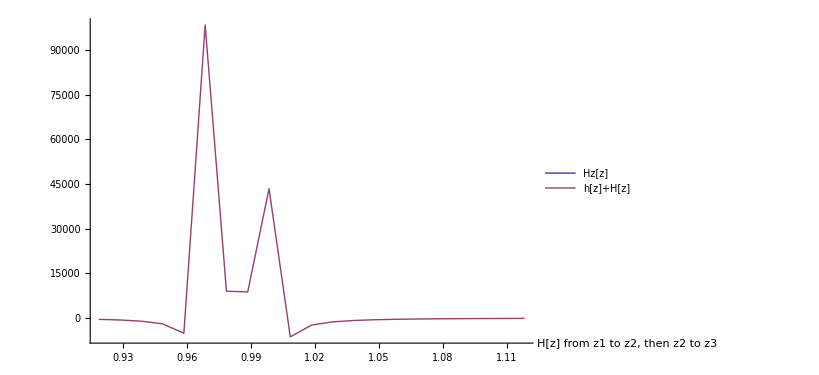

As y1[s] is in R_Le\L ∩ R_C, use alternative result for H[z]

zz=0.967659

h[zz]=-755604.

(λ1p ysm[zz])/((λ1m ysm[zz] + μ1) zz)=0.596545

Hz[lots]=-6.26533-6.04469×10^-8 ⅈ

0.235923

```mathematica
Wstar[0.0001,3,2,1,2,1.1,4]//PrintDebug
```

Checking a1, a2 values: {0.0672846,7.43112}

Checking y1, y2, y3, y4 values: {0.0112491,0.508628,4.28868,10.1883}

Checking y1[s] value: 0.422528

Checking z[y] values: {-0.0811667+1.02847×10^-9 ⅈ,0.499439+0. ⅈ,0.969887+0. ⅈ,-1.09532+1.32347×10^-8 ⅈ}

y1[s] is inside R_L

Solution to Fredholm equation:

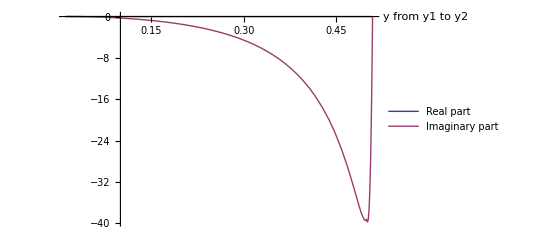

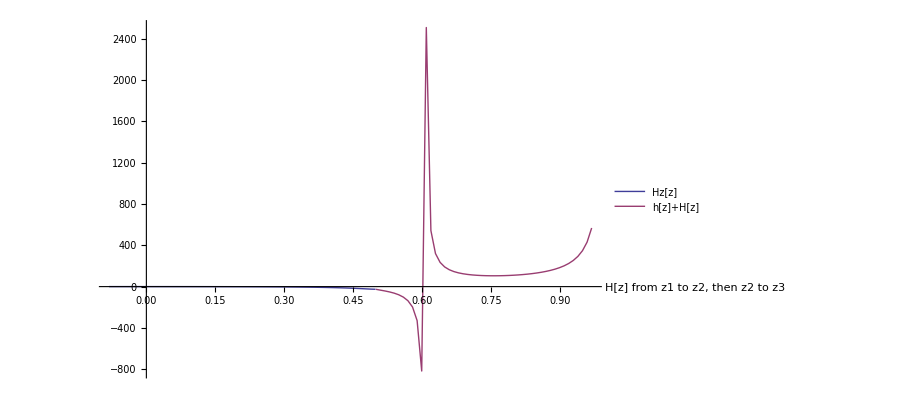

As y1[s] is in R_L, use equation [19] for H[z]

Hz[zz]=-11.5784+0. ⅈ

(λ1p ysm[zz])/((λ1m ysm[zz] + μ1) zz)=0.606887

0.0000115402

```mathematica
Wstar[0.0001,3,2,1,2,5.1,4]//PrintDebug
```

Checking a1, a2 values: {0,6.35821}

Checking y1, y2, y3, y4 values: {0,0.281289,3.43743,8.9977}

Checking y1[s] value: 0.612228

Checking z[y] values: {0.+0. ⅈ,0.493671+0. ⅈ,1.02712+0. ⅈ,-1.13658+0. ⅈ}

y1[s] is inside R_Le\L ∩ R_C

Solution to Fredholm equation:

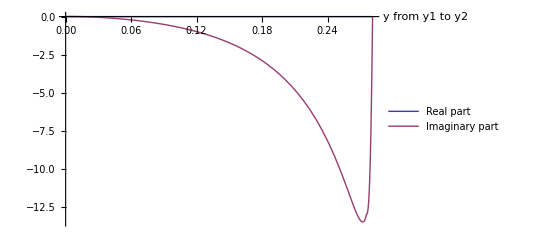

As y1[s] is in R_Le\L ∩ R_C, use alternative result for H[z]

zz=0.612228

h[zz]=-159338.

(λ1p ysm[zz])/((λ1m ysm[zz] + μ1) zz)=0.415255

Hz[lots]=-3.81612+0. ⅈ

-0.3945

```mathematica
Wstar[0.0001,3,2,0,2,2.9,4]//PrintDebug
```

Checking a1, a2 values: {0,7.19417}

Checking y1, y2, y3, y4 values: {0,0.352918,4.11159,9.92383}

Checking y1[s] value: 0.441169

Checking z[y] values: {0.+0. ⅈ,0.438516+5.41286×10^-9 ⅈ,0.973211+0. ⅈ,-1.09904+0. ⅈ}

y1[s] is inside R_Le\L ∩ R_C

Solution to Fredholm equation:

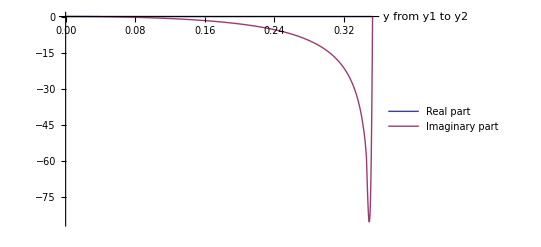

As y1[s] is in R_Le\L ∩ R_C, use alternative result for H[z]

zz=0.441169

h[zz]=-230714.

(λ1p ysm[zz])/((λ1m ysm[zz] + μ1) zz)=0.435898

Hz[lots]=-42.242+0. ⅈ

0.470004

```mathematica
Wstar[0.0001,3,2,0,2,4.8,4]//PrintDebug
```

```mathematica
ProbabilityOfNotBeingKilled[3,2,0,2,4.8,4]
```

0.470588

```mathematica
3/(2+4.9)
```

0.434783

Checking a1, a2 values: {0,7.23991}

Checking y1, y2, y3, y4 values: {0,0.355064,4.151,9.97374}

Checking y1[s] value: 0.434775

Checking z[y] values: {0.+0. ⅈ,0.43574+5.31224×10^-9 ⅈ,0.971219+1.80593×10^-8 ⅈ,-1.09736+0. ⅈ}

y1[s] is inside R_L

Solution to Fredholm equation:

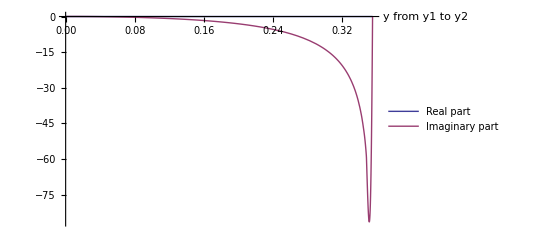

As y1[s] is in R_L, use equation [19] for H[z]

Hz[zz]=-43.2571+0. ⅈ

0.475283

```mathematica
Wstar[0.0001,3,2,0,2,4.9,4]//PrintDebug
```

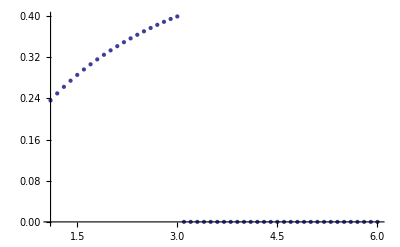

```mathematica
ListPlot[%120]
```

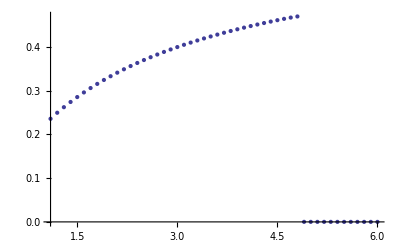

```mathematica
ListPlot[%118]
```

Checking a1, a2 values: {0.0721722,6.92788}

Checking y1, y2, y3, y4 values: {0.0135833,0.495795,3.85092,9.63981}

Checking y1[s] value: 0.49999

Checking z[y] values: {-0.100592+0. ⅈ,0.545874+0. ⅈ,0.993609+0. ⅈ,-1.11457+0. ⅈ}

y1[s] is inside R_L

Solution to Fredholm equation:

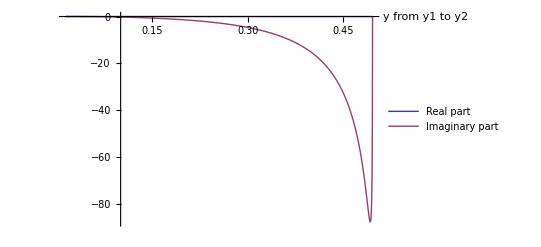

As y1[s] is in R_L, use equation [19] for H[z]

Hz[zz]=-31.5668-1.32059×10^-7 ⅈ

0.0000350739

```mathematica
Wstar[0.0001,3,2,1,2,4,4]//PrintDebug
```

Checking a1, a2 values: {0.0721722,6.92788}

Checking y1, y2, y3, y4 values: {0.0135833,0.495795,3.85092,9.63981}

Checking y1[s] value: 0.49999

Checking z[y] values: {-0.100592+0. ⅈ,0.545874+0. ⅈ,0.993609+0. ⅈ,-1.11457+0. ⅈ}

y1[s] is inside R_L

Solution to Fredholm equation:

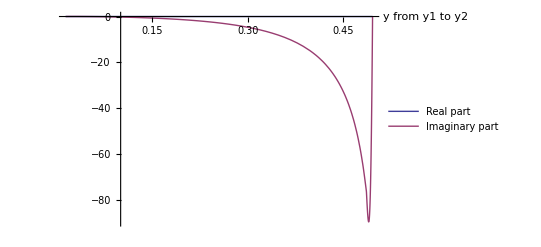

As y1[s] is in R_L, use equation [19] for H[z]

Hz[zz]=-28.8588-1.11745×10^-6 ⅈ

0.000032065

```mathematica
Wstar[0.0001,3,2,1,2,4,4]//PrintDebug
```

Checking a1, a2 values: {0,6.83338}

Checking y1, y2, y3, y4 values: {0,0.330718,3.80832,9.52773}

Checking y1[s] value: 0.49999

Checking z[y] values: {0.+0. ⅈ,0.461349+0. ⅈ,0.991716+3.24511×10^-8 ⅈ,-1.11344+2.06822×10^-8 ⅈ}

y1[s] is inside R_Le\L ∩ R_C

Solution to Fredholm equation:

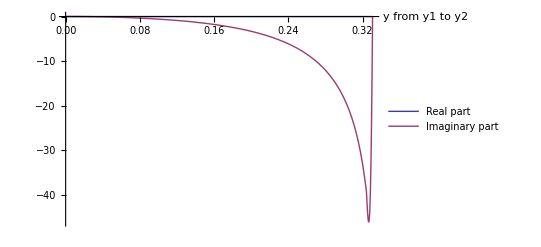

As y1[s] is in R_Le\L ∩ R_C, use alternative result for H[z]

zz=0.49999

h[zz]=-199969.

(λ1p ysm[zz])/((λ1m ysm[zz] + μ1) zz)=0.428572

Hz[lots]=-15.8625-9.27346×10^-7 ⅈ

0.444409

```mathematica
Wstar[0.0001,3,2,0,2,4,4]//PrintDebug
```

```mathematica
Table[{μ1,Wstar[0.0001,3,2,0,2,μ1,4]},{μ1,1.1,6,0.1}]
```

{{1.1,0.235925},{1.2,0.249692},{1.3,0.262424},{1.4,0.27436},{1.5,0.285595},{1.6,0.296196},{1.7,0.30622},{1.8,0.315713},{1.9,0.324718},{2.,0.333271},{2.1,0.341406},{2.2,0.349152},{2.3,0.356538},{2.4,0.363588},{2.5,0.370325},{2.6,0.376768},{2.7,0.382937},{2.8,0.388848},{2.9,0.394519},{3.,0.399962},{3.1,0.405192},{3.2,0.41022},{3.3,0.415059},{3.4,0.419718},{3.5,0.424208},{3.6,0.428537},{3.7,0.432715},{3.8,0.436748},{3.9,0.440644},{4.,0.444409},{4.1,0.448051},{4.2,0.451573},{4.3,0.454981},{4.4,0.458277},{4.5,0.461463},{4.6,0.464532},{4.7,0.467452},{4.8,0.470004},{4.9,0.0000874022},{5.,0.0000831232},{5.1,0.0000768557},{5.2,0.0000699306},{5.3,0.0000630554},{5.4,0.0000566047},{5.5,0.0000507515},{5.6,0.0000455475},{5.7,0.0000409755},{5.8,0.0000369839},{5.9,0.0000335073},{6.,0.0000304786}}

```mathematica
Wstar[s_,λ1p_:3,λ1m_:2,λ2p_:0,λ2m_:2,μ1_:2,μ2_:1]
```

```mathematica
Table[{μ1,-(Wstar[0.0002,1,1,0,1,μ1,4]-Wstar[0.0001,1,1,0,1,μ1,4])/0.0001},{μ1,1.1,5,0.5}]
```

$Aborted

```mathematica
Table[{μ1,-(Wstar[0.0002,1,0.00001,0,0.00001,μ1,4]-Wstar[0.0001,1,0.00001,0,0.00001,μ1,4])/0.0001},{μ1,1.1,5,0.5}]
```

{{1.1,10.3013},{1.6,1.99908},{2.1,1.24274},{2.6,0.961633},{3.1,0.837037},{3.6,1.24377},{4.1,-12.035-0.0000439637 ⅈ},{4.6,-2.57498}}

```mathematica
Table[{μ1,-(Wstar[0.0002,1,0.00001,0,0.00001,μ1,4]-Wstar[0.0001,1,0.00001,0,0.00001,μ1,4])/0.0001},{μ1,1.1,5,0.1}]
```

{{1.1,10.3013},{1.2,5.32506},{1.3,3.66288},{1.4,2.83117},{1.5,2.33195},{1.6,1.99908},{1.7,1.76129},{1.8,1.58296},{1.9,1.44429},{2.,1.3334},{2.1,1.24274},{2.2,1.16728},{2.3,1.10356},{2.4,1.04914},{2.5,1.00225},{2.6,0.961633},{2.7,0.926427},{2.8,0.896127},{2.9,0.870647},{3.,0.850466},{3.1,0.837037},{3.2,0.833643},{3.3,0.847242},{3.4,0.892504},{3.5,1.00102},{3.6,1.24377},{3.7,1.79509-1.28873×10^-6 ⅈ},{3.8,3.17692},{3.9,7.93278+0.0000152349 ⅈ},{4.,-2.51507},{4.1,-2.35827-0.0000439637 ⅈ},{4.2,-2.10359-6.58861×10^-6 ⅈ},{4.3,-1.83515},{4.4,-1.58639},{4.5,-1.36952},{4.6,-1.18621},{4.7,-1.03344},{4.8,-0.906639},{4.9,-0.80121},{5.,-0.713095}}

```mathematica
Table[{μ1,1/(μ1-1) + 1/(4-1)},{μ1,1.1,5,0.1}]
```

{{1.1,10.3333},{1.2,5.33333},{1.3,3.66667},{1.4,2.83333},{1.5,2.33333},{1.6,2.},{1.7,1.7619},{1.8,1.58333},{1.9,1.44444},{2.,1.33333},{2.1,1.24242},{2.2,1.16667},{2.3,1.10256},{2.4,1.04762},{2.5,1.},{2.6,0.958333},{2.7,0.921569},{2.8,0.888889},{2.9,0.859649},{3.,0.833333},{3.1,0.809524},{3.2,0.787879},{3.3,0.768116},{3.4,0.75},{3.5,0.733333},{3.6,0.717949},{3.7,0.703704},{3.8,0.690476},{3.9,0.678161},{4.,0.666667},{4.1,0.655914},{4.2,0.645833},{4.3,0.636364},{4.4,0.627451},{4.5,0.619048},{4.6,0.611111},{4.7,0.603604},{4.8,0.596491},{4.9,0.589744},{5.,0.583333}}

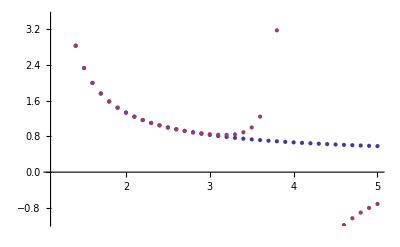

```mathematica
ListPlot[{%325,%321}]
```

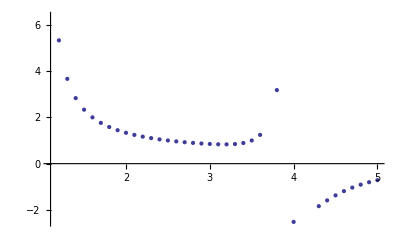

```mathematica
ListPlot[%321]
```

```mathematica
Table[{μ1,-(Wstar[0.0002,3,2,0,2,μ1,4]-Wstar[0.0001,3,2,0,2,μ1,4])/0.0001},{μ1,1.1,6,0.1}]
```

{{1.1,6.30786},{1.2,3.07401},{1.3,2.01535},{1.4,1.49845},{1.5,1.19599},{1.6,0.999346},{1.7,0.862311},{1.8,0.761983},{1.9,0.685766},{2.,0.626183},{2.1,0.578526},{2.2,0.539691},{2.3,0.507553},{2.4,0.480611},{2.5,0.457779},{2.6,0.438251},{2.7,0.421422},{2.8,0.406828},{2.9,0.394113},{3.,0.383005},{3.1,0.373296},{3.2,0.364838},{3.3,0.357537},{3.4,0.351363},{3.5,0.346359},{3.6,0.342679},{3.7,0.340644},{3.8,0.340847},{3.9,0.344342},{4.,0.35299},{4.1,0.370084},{4.2,0.401548},{4.3,0.458321},{4.4,0.561564},{4.5,0.755734},{4.6,1.14934},{4.7,2.09515-7.25213×10^-6 ⅈ},{4.8,5.84633-0.0000680497 ⅈ},{4.9,-0.871493},{5.,-0.828719-0.0000238977 ⅈ},{5.1,-0.766101-3.52323×10^-6 ⅈ},{5.2,-0.696928-1.74272×10^-6 ⅈ},{5.3,-0.628257},{5.4,-0.56383},{5.5,-0.505378},{5.6,-0.453416},{5.7,-0.407771},{5.8,-0.367927},{5.9,-0.33323},{6.,-0.303009}}

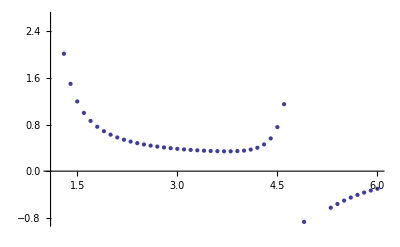

```mathematica
ListPlot[%319]
```

```mathematica
Table[{μ1,μ1*4/((2+μ1)*(2+4))},{μ1,1.1,6,0.1}]//N
```

{{1.1,0.236559},{1.2,0.25},{1.3,0.262626},{1.4,0.27451},{1.5,0.285714},{1.6,0.296296},{1.7,0.306306},{1.8,0.315789},{1.9,0.324786},{2.,0.333333},{2.1,0.341463},{2.2,0.349206},{2.3,0.356589},{2.4,0.363636},{2.5,0.37037},{2.6,0.376812},{2.7,0.382979},{2.8,0.388889},{2.9,0.394558},{3.,0.4},{3.1,0.405229},{3.2,0.410256},{3.3,0.415094},{3.4,0.419753},{3.5,0.424242},{3.6,0.428571},{3.7,0.432749},{3.8,0.436782},{3.9,0.440678},{4.,0.444444},{4.1,0.448087},{4.2,0.451613},{4.3,0.455026},{4.4,0.458333},{4.5,0.461538},{4.6,0.464646},{4.7,0.467662},{4.8,0.470588},{4.9,0.47343},{5.,0.47619},{5.1,0.478873},{5.2,0.481481},{5.3,0.484018},{5.4,0.486486},{5.5,0.488889},{5.6,0.491228},{5.7,0.493506},{5.8,0.495726},{5.9,0.49789},{6.,0.5}}

```mathematica
(1.5*4)/((2+1.5)(2+4))//N
```

0.285714

```mathematica
Wstar[0.0001,3,2,0,2,1.5,4]
```

0.285595

```mathematica
Wstar[0.00001]
```

0.166662

This looks encouraging -- when negative job rates are small, the probability of not being killed is nearly 1.

```mathematica
-(Wstar[0.000002,3,0.00001,0,0.00001,5,6]-Wstar[0.000001,3,0.00001,0,0.00001,5,6])/0.000001
```

0.895904

```mathematica
1/2 + 1/3 //N
```

0.833333

Plotting Wstar[s]

```mathematica
Table[{i,Wstar[i]},{i,0.01,1,0.01}]
```

{{0.01,0.161759},{0.02,0.157067},{0.03,0.152573},{0.04,0.148265},{0.05,0.144129},{0.06,0.140152},{0.07,0.136324},{0.08,0.132634},{0.09,0.12907},{0.1,0.125626},{0.11,0.12229},{0.12,0.119056+3.35792×10^-9 ⅈ},{0.13,0.115914+3.71903×10^-9 ⅈ},{0.14,0.112858+4.10443×10^-9 ⅈ},{0.15,0.10988},{0.16,0.106973},{0.17,0.10413},{0.18,0.101344},{0.19,0.0986085},{0.2,0.0959169},{0.21,0.0932624},{0.22,0.0906382},{0.23,0.0880374},{0.24,0.0854527},{0.25,0.0828765},{0.26,0.0803005},{0.27,0.0777158},{0.28,0.0751122},{0.29,0.0724778},{0.3,0.0697982},{0.31,0.067054},{0.32,0.0642156+4.69799×10^-8 ⅈ},{0.33,0.062831},{0.34,0.063019},{0.35,0.0630604},{0.36,0.0629902},{0.37,0.0628303},{0.38,0.062597+1.02995×10^-8 ⅈ},{0.39,0.0623028},{0.4,0.0619579+8.29794×10^-9 ⅈ},{0.41,0.0615704},{0.42,0.0611475},{0.43,0.0606949},{0.44,0.0602177},{0.45,0.0597201},{0.46,0.0592058},{0.47,0.058678},{0.48,0.0581394+4.28095×10^-9 ⅈ},{0.49,0.0575925+3.9938×10^-9 ⅈ},{0.5,0.0570394+3.73359×10^-9 ⅈ},{0.51,0.0564817},{0.52,0.0559212},{0.53,0.0553591},{0.54,0.0547967+2.90284×10^-9 ⅈ},{0.55,0.0542351+2.73648×10^-9 ⅈ},{0.56,0.053675+2.58324×10^-9 ⅈ},{0.57,0.0531173},{0.58,0.0525627+3.26819×10^-9 ⅈ},{0.59,0.0520118},{0.6,0.051465},{0.61,0.0509227},{0.62,0.0503855+1.87531×10^-9 ⅈ},{0.63,0.0498535},{0.64,0.049327},{0.65,0.0488062},{0.66,0.0482914+2.67836×10^-9 ⅈ},{0.67,0.0477827+1.47683×10^-9 ⅈ},{0.68,0.0472801},{0.69,0.0467838+1.35033×10^-9 ⅈ},{0.7,0.0462938},{0.71,0.0458102},{0.72,0.0453331},{0.73,0.0448623},{0.74,0.044398},{0.75,0.0439401+1.05061×10^-9 ⅈ},{0.76,0.0434885},{0.77,0.0430433+9.71429×10^-10 ⅈ},{0.78,0.0426044+9.3495×10^-10 ⅈ},{0.79,0.0421718},{0.8,0.0417453},{0.81,0.041325},{0.82,0.0409107+8.0677×10^-10 ⅈ},{0.83,0.0405025},{0.84,0.0401001},{0.85,0.0397036},{0.86,0.0393129},{0.87,0.0389279+6.7879×10^-10 ⅈ},{0.88,0.0385484+6.56668×10^-10 ⅈ},{0.89,0.0381745+6.35549×10^-10 ⅈ},{0.9,0.0378061},{0.91,0.037443+5.96093×10^-10 ⅈ},{0.92,0.0370851},{0.93,0.0367325+7.9197×10^-10 ⅈ},{0.94,0.036385},{0.95,0.0360424},{0.96,0.0357049},{0.97,0.0353722+4.96553×10^-10 ⅈ},{0.98,0.0350442+4.82287×10^-10 ⅈ},{0.99,0.034721},{1.,0.0344023}}

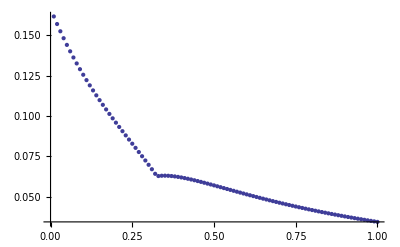

```mathematica
ListPlot[Re[%]]
```

Mean response time

```mathematica
-(Wstar[2*0.0001,3,0.01,0,0.01,5,6]-Wstar[0.0001,3,0.01,0,0.01,5,6])/0.0001
```

0.888278

### Zhan testing: ysp is always the smallest, ysm the largest

```mathematica
(*Laplace transform at transform parameter value s*)
Wstar2[s_,λ1p_:3,λ1m_:2,λ2p_:0,λ2m_:2,μ1_:2,μ2_:1]:=Module[{y1s,λ1,λ2,ρ1,ρ2,α,a1,a2,y,y1,y2,y3,y4,yp,ym,ysm,zp,zm,zsm,lambdaz,Kpartz,gfun,fz,YYz,Cz,Kernelz,Hz,h,Gtilde},
If[Im[s]≠0||s<0,Return["ERROR: s must be real and non-negative"]];
λ1=λ1p+λ1m;λ2=λ2p+λ2m;(*p.226*)ρ1=λ1p/(λ1m+μ1);ρ2=(μ1 ρ1+λ2p)/(λ2m+μ2);(*p.227*)
If[ρ1≥1,Return["ERROR: Node 1 utilization ≥1"]];
If[ρ2≥1,Return["ERROR: Node 2 utilization ≥1"]];
α=s+λ1+λ2+μ1+μ2(1-ρ2);(*p.234*)
{a1,a2}=y/.NSolve[α y-λ2m y^2-λ2p==0,y]//Chop;(*Lemma 1.1*)
debugPrint["Checking a1, a2 values: ",{a1,a2}];

{y1,y2,y3,y4}=y/.NSolve[(α y-λ2m y^2-λ2p)^2-4λ1p y(λ1m y+μ1)==0,y]//Chop;(*Lemma 1.1*)
debugPrint["Checking y1, y2, y3, y4 values: ",{y1,y2,y3,y4}];

yp[z_]:=(α z-λ1p-λ1m z^2+Sqrt[(α z-λ1p-λ1m z^2)^2-4λ2m z^2(λ2p+μ1 z)])/(2λ2m z);(*p.235, [13]*)
ym[z_]:=(α z-λ1p-λ1m z^2-Sqrt[(α z-λ1p-λ1m z^2)^2-4λ2m z^2(λ2p+μ1 z)])/(2λ2m z);(*p.235, [13]*)
ysm[z_]:=If[Abs[yp[z]]≤Abs[ym[z]],yp[z],ym[z]]; (*choose smallest modulus value*)
ylm[z_]:=If[Abs[yp[z]]≤Abs[ym[z]],ym[z],yp[z]]; (*choose largest modulus value*)
zp[y_]:=(α y-λ2m y^2-λ2p+ⅈ Sqrt[4λ1p y(λ1m y+μ1)-(α y-λ2m y^2-λ2p)^2])/(2(λ1m y+μ1));(*p. 238, [18]*)
zm[y_]:=(α y-λ2m y^2-λ2p-ⅈ Sqrt[4λ1p y(λ1m y+μ1)-(α y-λ2m y^2-λ2p)^2])/(2(λ1m y+μ1));(*p. 238, [18]*)
zsm[y_]:=If[Abs[zp[y]]≤Abs[zm[y]],zp[y],zm[y]]; (*choose smallest modulus value*)
zlm[y_]:=If[Abs[zp[y]]≤Abs[zm[y]],zm[y],zp[y]]; (*choose largest modulus value*)
y1s=Min[y/.Solve[λ1m y^2-(s+λ1+μ1(1-ρ1))y+λ1p==0,y]]//N;(*p.229 Theorem 1*)
If[y1s≥1,Return["ERROR: y1[s]≥1"]];
debugPrint["Checking y1[s] value: ",y1s];
debugPrint["Checking z[y] values: ",{zsm[y1],zsm[y2],zsm[y3],zsm[y4]}];

ysvals=yy/.NSolve[s+λ1+λ2+μ1+μ2(1-ρ2)-λ1p/y1s-λ1m y1s-λ2p/yy-λ2m yy-μ1 y1s/yy==0,yy];(*p.240*)
ysval=If[Abs[ysvals[[1]]]≤Abs[ysvals[[2]]],ysvals[[1]],ysvals[[2]]];
If[(λ1p ysval)/((λ1m ysval+μ1)y1s)>y1s,debugPrint["y1[s] is inside R_L"],debugPrint["y1[s] is inside R_Le\\L ∩ R_C"]];
n=100;
(*Terms for Fredholm integral equation specified in equation [17], p.238*)
lambdaz=-μ1 λ2m/(2π ⅈ);
Kpartz[y_,t_]:=((λ1m y+μ1)(zsm[y]-zlm[y]))/(λ1p μ1^2+(λ2m y t-λ2p)(λ2m t(λ1m y+μ1)+μ1(λ2m y-α)-λ1m λ2p));
gfun[y_]:=μ2 y/(1-y)(zsm[y]/((1-zsm[y])(zsm[y]-ρ1))-zlm[y]/((1-zlm[y])(zlm[y]-ρ1)));(*p.238*)
fz=FredholmKind2[{y1,y2,lambdaz,Kpartz,gfun},n,Method->Automatic];
debugPrint["Solution to Fredholm equation:"];
debugPrint[Plot[{Re[fz[yyy]],Im[fz[yyy]]},{yyy,y1,y2},{PlotStyle->Thick,PlotLegends->{"Real part","Imaginary part"},AxesLabel->{"y from y1 to y2"},PlotRange->All}]];
YYz[y_]:=D[zsm[y],y]/zsm[y] + D[zlm[y],y]/zlm[y];
Cz=NIntegrate[YYz[y]*fz[y]/(2*Pi*I),{y,y1,y2}]//Chop;
Kernelz[zz_,y_]:=D[zsm[y],y]/(zsm[y]-zz) + D[zlm[y],y]/(zlm[y]-zz);
Hz[zz_]:=Cz-NIntegrate[Kernelz[zz,y]*fz[y]/(2*Pi*I),{y,y1,y2}]//Chop;
h[zz_]:=μ2 ysm[zz]/(1-ysm[zz])(zz/((1-zz)(zz-ρ1))-((λ1p ysm[zz])/(zz(λ1m ysm[zz]+μ1)))/((1-(λ1p ysm[zz])/(zz(λ1m ysm[zz]+μ1)))((λ1p ysm[zz])/(zz(λ1m ysm[zz]+μ1))-ρ1)));(*p.234 using z^sigma from p.235*)
Gtilde[zz_]:=Block[{},(*For real valued z only*)
(*p.239, first case*)
If[zz> Re[zsm[y1]]&&zz<Re[zsm[y2]],
debugPrint["As y1[s] is in R_L, use equation [19] for H[z]"];
Return[(zz-ρ1)/(zz(μ1 zz+λ2p))Hz[zz]]];
(*p.239, second case*)
If[((zz<Re[zsm[y1]]&&zz>Re[zsm[y4]])||(zz>Re[zsm[y2]]&&zz<Re[zsm[y3]]))&&(zz<ρ1),(*RC defined on p.234*)
debugPrint["As y1[s] is in R_Le\\L ∩ R_C, use alternative result for H[z]"];
debugPrint["zz=",zz];
debugPrint["h[zz]=",h[zz]];
debugPrint["(λ1p ysm[zz])/((λ1m ysm[zz] + μ1) zz)=",(λ1p ysm[zz])/((λ1m ysm[zz]+μ1)zz)];
debugPrint["Hz[lots]=",Hz[(λ1p ysm[zz])/((λ1m ysm[zz]+μ1)zz)]];

Return[(zz-ρ1)/(zz(μ1 zz+λ2p))(h[zz]+Hz[(λ1p ysm[zz])/((λ1m ysm[zz]+μ1)zz)])];
(*Catch remaining values*)
Return["ERROR: Unexpected value for y1[s] (outside considered region)."]];
];
(*Return W*(s),p.239*)
Return[((1-ρ1)(1-ρ2)μ1 y1s)/λ1p Gtilde[y1s]//Chop]; 
];
```

```mathematica
Wstar2[0.0001,3,2,0,2,4.9,4]//PrintDebug
```

Checking a1, a2 values: {0,7.23991}

Checking y1, y2, y3, y4 values: {0,0.355064,4.151,9.97374}

Checking y1[s] value: 0.434775

Checking z[y] values: {0.+0. ⅈ,0.43574+5.31224×10^-9 ⅈ,0.971219+1.80593×10^-8 ⅈ,-1.09736+0. ⅈ}

y1[s] is inside R_L

Solution to Fredholm equation:

-Graphics-

As y1[s] is in R_L, use equation [19] for H[z]

0.0000874022